```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->LightGray]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["eval*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[ImagEv[i]=Table[vec[i][[j,2]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
```

```mathematica
Table[ReEv[i],{i,1,Length[data]}]
```

{{-4024.67,-2268.22,-740.609,-586.673,-345.033,-299.998,-230.357,-189.421,-148.237,-1.4458,-7.61782,-18.7218,-34.7601,-55.7331,-81.6408,-112.484}}

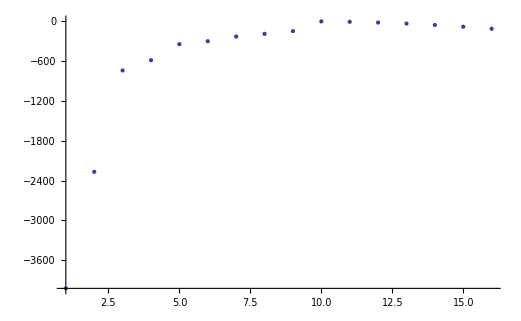

```mathematica
ListPlot[Table[ReEv[i],{i,1,Length[data]}],PlotRange->All]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_Spectral/V"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/V

```mathematica
ClearAll["Global`*"]
```

```mathematica
data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
Length[data]
```

16

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,Length[data]+2}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,Length[data]+2}],{i,1,Length[data]}];
```

```mathematica
Length[data]
```

16

```mathematica
Y[i_]:= Cos[i Pi/(Length[data]+1)];
```

```mathematica
xs=Sort[Table[N[Y[i]],{i,0,Length[data]+1}]];
```

```mathematica
Length[xs]
```

18

```mathematica
xs+1
```

{0.,0.0218524,0.0864545,0.190983,0.330869,0.5,0.690983,0.895472,1.10453,1.30902,1.5,1.66913,1.80902,1.91355,1.97815,2.}

```mathematica
Do[RealPairs[i]=Thread[{xs+1,realvec[i]}],{i,1,Length[data]}]
```

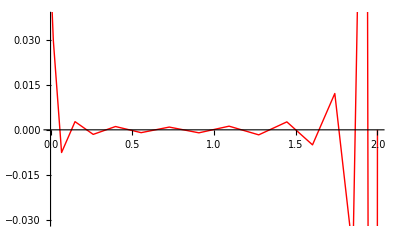
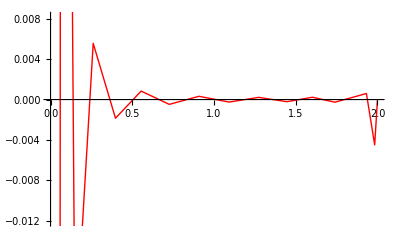
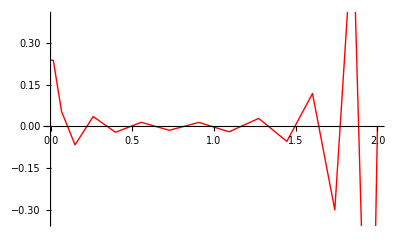
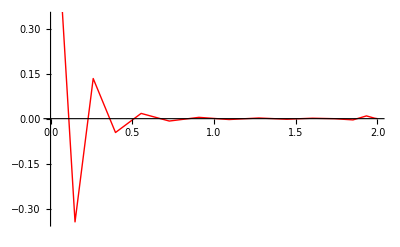
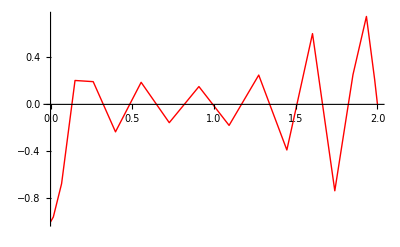
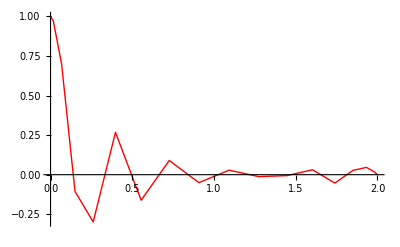
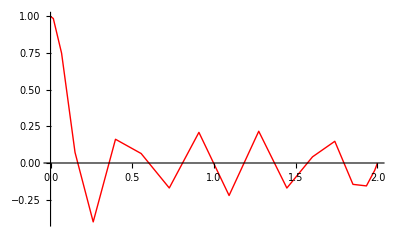
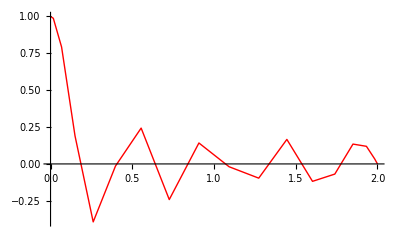

```mathematica
Table[ListPlot[RealPairs[i],Joined->True,PlotStyle->Red],{i,1,Length[data]}]
```

```mathematica
l1=ListPlot[RealPairs[12],Joined->True,PlotStyle->Red]
```

-Graphics-

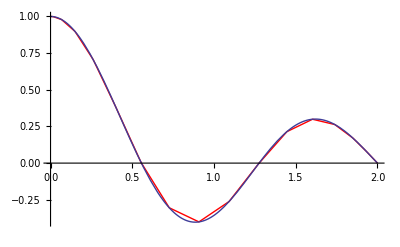

```mathematica
Show[l1,p2]
```

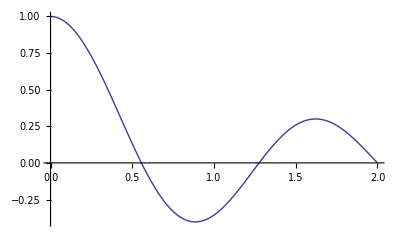

```mathematica
p2=Plot[BesselJ[0,BesselJZero[0,3]x/2],{x,0,2}]
```

```mathematica
(* only first two have true nonzero eigenvalues *)
```

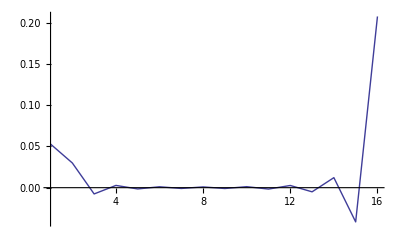
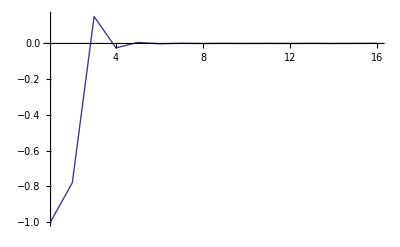
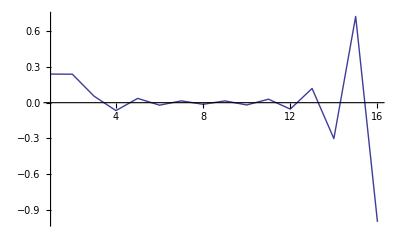
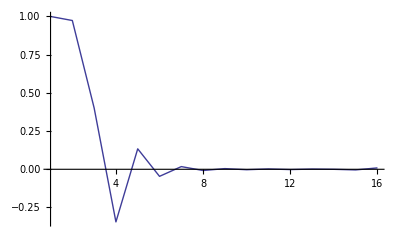
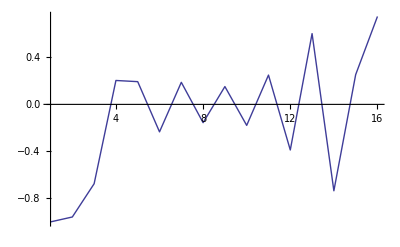
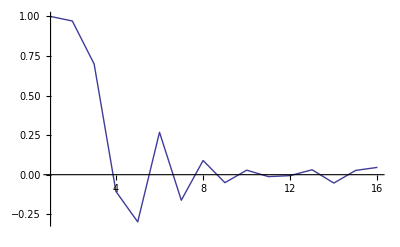
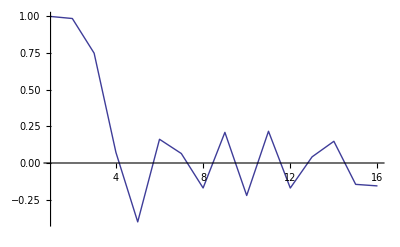
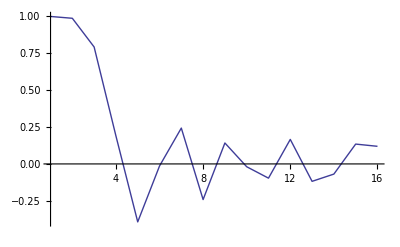

```mathematica
Table[ListPlot[realvec[j],PlotRange->All,Joined->True],{j,1,Length[data]}]
```